# Introdução à Física Computacional I (2023.2)

## Aula 3: listas; funções de iteração; laços; vetores e matrizes; funções e listas Boa parte de lista em 2.4 e matrizes em 2.1

## Listas

Tanto na linguagem Wolfram quanto em várias outras linguagens de programação, como Python, uma forma básica de colecionar objetos (números, variáveis, atribuições temporárias etc.) são as listas. No Mathematica, listas são delimitadas por chaves, como já mencionamos na aula passada.

```mathematica
lista1={4,3,2,1,a,b,c}
```

{4,3,2,1,a,b,c}

```mathematica
lista2={a,x,y}
```

{a,x,y}

```mathematica
lista3={1,4,9,16}
```

{1,4,9,16}

Existem muitas funções intrínsecas para manipular listas, algumas das quais discutiremos a seguir.

A função Join cria uma única lista combinando duas ou mais listas:

```mathematica
Join[lista1,lista2,lista3]
```

{4,3,2,1,a,b,c,a,x,y,1,4,9,16}

Note que os elementos duplicados não são removidos pela função Join. Caso queira fazer isso, gerando uma lista ordenada, use a função Union:

```mathematica
Union[lista1,lista2,lista3]
```

Union::normal: Nonatomic expression expected at position 1 in lista1∪lista2∪lista3.

lista1∪lista2∪lista3

A função Intersection retorna uma lista ordenada de elementos que são comuns a todas as listas utilizadas como argumentos:

```mathematica
Intersection[lista1,lista2]
```

{a}

```mathematica
Intersection[lista1,lista3]
```

{1,4}

```mathematica
Intersection[lista1,lista2,lista3]
```

{}

Uma lista pode conter elementos que são eles próprios outras listas:

```mathematica
lista4={1,3,5,7,lista2}
```

{1,3,5,7,{a,x,y}}

Note que, na criação da lista4, as chaves presentes na lista2 não são removidas. Caso queira removê-las (o que vai ser importante, por exemplo, para fazer gráficos), use a função Flatten:

```mathematica
Flatten[lista4](*serve para retirar chaves internas*)
```

{1,3,5,7,a,x,y}

A função AppendTo adiciona elementos a uma lista:

```mathematica
lista5={1,3,5,7};
```

```mathematica
AppendTo[lista5,9] (* O segundo argumento é o elemento a adicionar *)
```

{1,3,5,7,9}

Note que a lista5 foi alterada:

```mathematica
lista5
```

{1,3,5,7,9}

A função Drop retira elementos de uma lista:

```mathematica
Drop[lista5,{1,2}] (* O segundo argumento indica  as posições do primeiro e do último elemento a remover *)
```

{5,7,9}

Atenção: a linguagem Wolfram utiliza 1 (e não 0) para rotular a posição do primeiro elemento.

Note que a lista5 não foi alterada:

```mathematica
lista5
```

```mathematica
{1,3,5,7,9}
```

{1,3,5,7,9}

Se quiser fazer isso, utilize a atualização

```mathematica
lista5=Drop[lista5,{1,2}]
```

{5,7,9}

Note que Drop funciona com base nas posições e não nos valores dos elementos. Caso queira descobrir todas as posições de uma lista que contêm um determinado elemento, utilize a função Position:

```mathematica
Position[{1,2,1,3,1,4},1]
```

{{1},{3},{5}}

Para exibir elementos de uma lista, utilize a função Part, que tem a alternativa compacta [[]], conforme os exemplos a seguir:

```mathematica
lista6={1,3,5,7,9};
```

```mathematica
(*Perceba que em Python a referenciação de um certo elemento de uma lista se dá em parênteses*)
```

```mathematica
lista6[[3]] (* Fornece o terceiro elemento da lista6  *)
```

5

```mathematica
lista6[[2;;4]]  (* Fornece uma lista contendo os elementos nas posições 2 a 4 da lista6 *)
```

{3,5,7}

```mathematica
lista6[[-2]] (* Fornece o penúltimo elemento da lista6 *)
```

7

Uma forma conveniente de armazenar dados experimentais (por exemplo, medidas do comprimento de uma barra como função da temperatura) é por meio de uma lista de pares ordenados:

```mathematica
lista7={{25,29.9},{26,30.5},{27,31.1},{28,31.5}}
```

{{25,29.9},{26,30.5},{27,31.1},{28,31.5}}

Em um lista de pares ordenados (um exemplo de uma “lista de listas”), você pode utilizar Part para exibir um elemento específico de uma lista interna (aqui cada par ordenado), indicando a posição dessa lista na lista externa (aqui a lista7) e a posição do elemento na lista interna. Por exemplo, para saber o segundo elemento no terceiro par ordenado da lista7:

```mathematica
lista7[[3,2]]
```

31.1

Caso queira produzir uma lista com os elementos na primeira posição de cada lista interna, você pode utilizar a especificação All:

```mathematica
lista7[[All,1]]
```

{25,26,27,28}

Para fazer um gráfico a partir de uma lista de pares ordenados, com o primeiro elemento de um par fornecendo a abscissa e o segundo, a ordenada, utilize a função ListPlot:

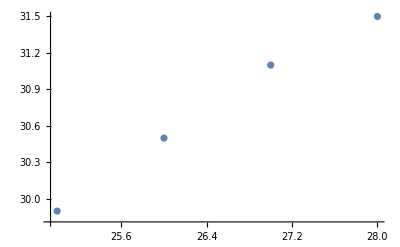

```mathematica
ListPlot[lista7]
```

Quando utilizada com uma lista simples, a função ListPlot trata os elementos da lista como ordenadas e adota para as abscissas a sequência de números naturais a partir do 1:

```mathematica
lista6
```

{1,3,5,7,9}

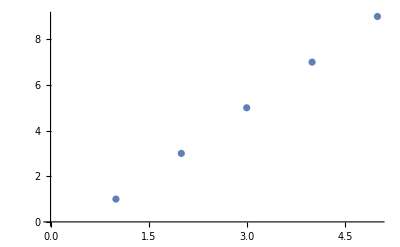

```mathematica
ListPlot[lista6]
```

## Funções de iteração e iteradores

Funções de iteração permitem repetir uma operação, seja da mesma maneira ou de forma ligeiramente diferente, e podem produzir listas como resultado. Vamos discutir algumas funções de iteração da linguagem Wolfram nos exemplos a seguir.

A função de iteração Range produz uma lista ordenada de números:

```mathematica
Range[10] (* Produz uma lista de inteiros de 1 até 10 *)
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Range[5,10]  (* Produz uma lista de inteiros de 5 até 10 *)
```

{5,6,7,8,9,10}

```mathematica
Range[10,5,-2]  (* Produz uma lista de inteiros de 10 até 5, com incremento -2 *)
```

{10,8,6}

```mathematica
Range[1,2,0.1] (* Produz uma lista de números reais de 1.0 até 2.0 com incremento de 0.1 *)
```

{1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.}

Várias funções de iteração utilizam especificadores de iteração, ou iteradores, que tomam a forma de listas cujo primeiro elemento indica a variável cujo valor será iterado, ou de listas de 1 único elemento constante. As funções a seguir exemplificam o uso de iteradores.

A função de iteração Table produz uma lista segundo regras definidas pelos argumentos:

```mathematica
Table[1/2^n,{n,4}] (* Produz uma lista das potências de 2 desde 1/2^1 até 1/2^4. O iterador {n,4} indica que n percorre os números inteiros de 1 a 4.  *)
```

{1/2,1/4,1/8,1/16}

```mathematica
Table[1/3^n,{n,0,4}]  (* Produz uma lista das potências de 3 desde 1/3^0 até 1/3^4. O iterador {n,0,4} indica que n percorre os números inteiros de 0 a 4. *)
```

{1,1/3,1/9,1/27,1/81}

```mathematica
Table[1/2^n,{n,0,7,3}]   (* Produz uma lista das potências de 2 desde 1/2^0 até 1/2^7, com incremento 3 na potência. O iterador {n,0,7,3} indica que n percorre os números inteiros de 0 a 7, de 3 em 3. *)
```

```mathematica
Table[b,{4}] (* Produz uma lista contendo 4 elementos iguais a 'b'. O iterador {4} indica que serão produzidos 4 valores iguais, nesse caso, ao primeiro argumento de Table. *)
```

Outra função de iteração útil é a função Do, cujo uso vamos ilustrar produzindo a sequência dos 101 primeiros números de Fibonacci. Vamos defini-los como “funções” que existem apenas para certos valores (nesse caso, inteiros) do argumento, um recurso do Mathematica que às vezes é útil.

```mathematica
f[0]=1; 
f[1]=1;
```

```mathematica
Do[f[k]=f[k-1]+f[k-2],{k,2,100}] 
f[100]
```

573147844013817084101

A atribuição no primeiro argumento da função Do foi repetida para todos os valores de k entre 2 e 100. Não há saída automática de cada atribuição, mas é possível visualizar os valores atribuídos com o auxílio da função Print:

```mathematica
Do[Print[f[k]],{k,0,8}]
```

1

1

f[2]

f[3]

f[4]

f[5]

f[6]

f[7]

f[8]

A função Do implementa explicitamente uma estrutura de programação conhecida como laço, essencial na construção de algoritmos computacionais. Voltaremos a discutir laços em aulas futuras.

Se quisermos produzir uma lista a partir dos valores calculados para os números de Fibonacci, podemos utilizar a função Table:

```mathematica
Table[f[k],{k,0,25}]
```

{1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181,6765,10946,17711,28657,46368,75025,121393}

## Funções e listas

A maioria das funções do Mathematica é “listável”, ou seja, pode receber uma lista como argumento, devolvendo como resultado uma outra lista contendo a aplicação da função separadamente a cada elemento. Vejamos exemplos:

```mathematica
{1,2,3}+2 (* Aplicando a função Plus *)
```

{3,4,5}

```mathematica
{1,2,3}^3 (* Aplicando a função Power *)
```

{1,8,27}

```mathematica
Sin[{π/6,π/4,π/3,π/2}] (* Aplicando a função seno *)
```

{1/2,1/(√2),(√3)/2,1}

Funções definidas pelo usuário podem não ser “listáveis”. Esse é o caso da função f que definimos há pouco:

```mathematica
f[{9,10}]
```

f[{9,10}]

Para esses casos, a função Map garante a aplicação a cada elemento da lista separadamente:

```mathematica
Map[f,{9,10}]
```

{55,89}

## Vetores e matrizes

No Mathematica, vetores e matrizes são definidos como listas. Um vetor é definido como uma lista simples:

```mathematica
vetor1={1,1/2,2}
```

{1,1/2,2}

Uma matriz é definida como uma lista de listas, cada uma representando uma linha da matriz, que nem um Python, porém neste lembre-se que as listas são em colchetes([]).

```mathematica
matriz1={{0,1},{1,0}}
```

{{0,1},{1,0}}

Para visualizar esses objetos na forma usual, utilizamos a função MatrixForm:

```mathematica
MatrixForm[vetor1]
```

(1
1/2
2)

```mathematica
MatrixForm[matriz1]
```

(0 | 1
1 | 0)

```mathematica
{{1,0,0},{0,1,0},{0,0,1}}//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

Há várias funções para lidar com vetores e matrizes. Vamos discutir a seguir algumas delas.

O produto escalar é invocado pela função Dot (ou simplesmente “.”):

```mathematica
Dot[{a,b,c},{x,y,z}]  (* O primeiro argumento é tratado como vetor linha e o segundo, como vetor coluna *)
```

a x+b y+c z

```mathematica
matriz1.{1,0}//MatrixForm
```

(0
1)

```mathematica
{{a,b},{c,d}}.{{e,f},{g,h}}//MatrixForm
```

(a e+b g | a f+b h
c e+d g | c f+d h)

A função Norm calcula a norma de um vetor (ou de um número complexo):

```mathematica
Norm[{x,y,z}]
```

√(Abs[x]^2+Abs[y]^2+Abs[z]^2)

```mathematica
Norm[1+I]
```

√2

A função Cross calcula o produto vetorial de dois vetores:

```mathematica
Cross[{1,2,1},{3,-1,1}]//MatrixForm
```

(3
2
-7)

A função Det calcula o determinante de uma matriz:

```mathematica
Det[{{a,b},{c,d}}]
```

-b c+a d

A função Tr calcula o traço de uma matriz:

```mathematica
Tr[{{a,b},{c,d}}]
```

a+d

A função Transpose calcula a transposta de uma matriz:

```mathematica
Transpose[{{a,b},{c,d}}]//MatrixForm
```

(a | c
b | d)

Em aulas futuras discutiremos outras funções relacionadas a matrizes.

A função Table também pode produzir uma matriz a partir de uma fórmula:

```mathematica
Table[x^m/(n*y),{m,4},{n,3}]
```

{{x/y,x/(2 y),x/(3 y)},{x^2/y,x^2/(2 y),x^2/(3 y)},{x^3/y,x^3/(2 y),x^3/(3 y)},{x^4/y,x^4/(2 y),x^4/(3 y)}}

```mathematica
MatrixForm[%]
```

(x/y | x/(2 y) | x/(3 y)
x^2/y | x^2/(2 y) | x^2/(3 y)
x^3/y | x^3/(2 y) | x^3/(3 y)
x^4/y | x^4/(2 y) | x^4/(3 y))

Finalmente, a função Transpose pode ser utilizada para transformar duas listas (por exemplo, uma de temperaturas, outra de comprimentos de uma barra) em uma lista de pares ordenados.

```mathematica
lista8x={25,26,27,28}; 
lista8y={29.9,30.5,31.1,31.5};
lista8xy={lista8x,lista8y}
lista8=Transpose[lista8xy]
```

{{25,26,27,28},{29.9,30.5,31.1,31.5}}

{{25,29.9},{26,30.5},{27,31.1},{28,31.5}}

```mathematica
ListPlot[lista8]
```

-Graphics-

## Exercícios no E-disciplinas